### Data and settings

```mathematica
data=Import[NotebookDirectory[]<>"\\control8.CSV","Data"];
myPlotSettings={ImageSize->Medium,Frame->True,Axes->False,PlotRange->All};
```

### Parse and plot data

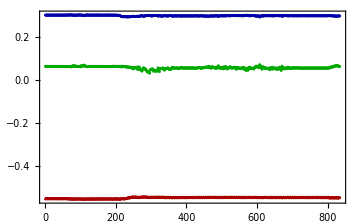

```mathematica
Bx=data[[2;;-1;;6]];
Bx=Flatten[Bx];
Bx=Function[x,ToExpression[StringTake[x,{4,-1}]]]/@Bx;
By=data[[3;;-1;;6]];
By=Flatten[By];
By=Function[x,ToExpression[StringTake[x,{4,-1}]]]/@By;
Bz=data[[4;;-1;;6]];
Bz=Flatten[Bz];
Bz=Function[x,ToExpression[StringTake[x,{4,-1}]]]/@Bz;
Show[{ListPlot[Bx,PlotStyle->Darker[Red]],ListPlot[By,PlotStyle->Darker[Green]],ListPlot[Bz,PlotStyle->Darker[Blue]]},Evaluate[myPlotSettings]]
```

### Get sensor bias

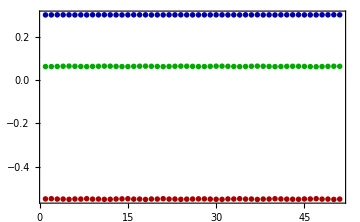

```mathematica
indexStart=10;
indexEnd=60;
BxUseful=Bx⟦indexStart;;indexEnd⟧;
ByUseful=By⟦indexStart;;indexEnd⟧;
BzUseful=Bz⟦indexStart;;indexEnd⟧;
Show[{ListPlot[BxUseful,PlotStyle->Darker[Red]],ListPlot[ByUseful,PlotStyle->Darker[Green]],ListPlot[BzUseful,PlotStyle->Darker[Blue]]},Evaluate[myPlotSettings]]
BxMean1=Mean[BxUseful];
ByMean1=Mean[ByUseful];
BzMean1=Mean[BzUseful];
```

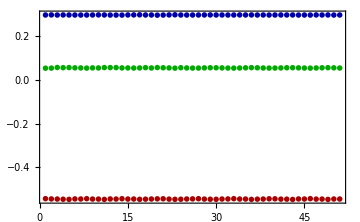

```mathematica
indexStart=700;
indexEnd=750;
BxUseful=Bx⟦indexStart;;indexEnd⟧;
ByUseful=By⟦indexStart;;indexEnd⟧;
BzUseful=Bz⟦indexStart;;indexEnd⟧;
Show[{ListPlot[BxUseful,PlotStyle->Darker[Red]],ListPlot[ByUseful,PlotStyle->Darker[Green]],ListPlot[BzUseful,PlotStyle->Darker[Blue]]},Evaluate[myPlotSettings]]
BxMean2=Mean[BxUseful];
ByMean2=Mean[ByUseful];
BzMean2=Mean[BzUseful];
```